```mathematica
SetDirectory[NotebookDirectory[]];
```

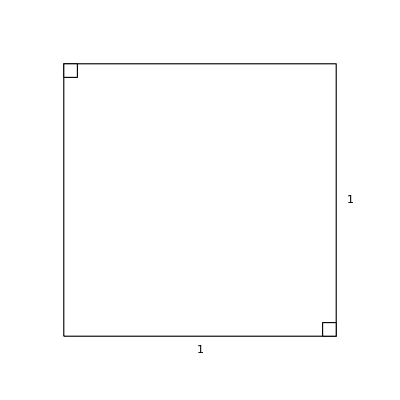

```mathematica
Show[
Graphics[{White,EdgeForm[Directive[Black,Thick]],Rectangle[{0,0},{1,1}]}],
Graphics[{White,EdgeForm[Directive[Black,Thick]],Rectangle[{0,1},{0.05,1-0.05}]}],
Graphics[{White,EdgeForm[Directive[Black,Thick]],Rectangle[{1,0},{1-0.05,0.05}]}],
PlotRange->{{-0.1,1.1},{-0.1,1.1}},
Epilog->{
Style[Text[1,{0.5,-0.05}],25],
Style[Text[1,{1+0.05,0.5}],25]
}]
Export[{"st1.pdf","st1.svg"},%];
```

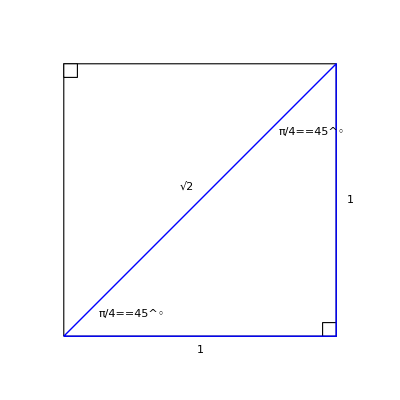

```mathematica
Show[
Graphics[{White,EdgeForm[Directive[Black,Thick]],Rectangle[{0,0},{1,1}]}],
Graphics[{White,EdgeForm[Directive[Black,Thick]],Rectangle[{0,1},{0.05,1-0.05}]}],
Graphics[{White,EdgeForm[Directive[Black,Thick]],Rectangle[{1,0},{1-0.05,0.05}]}],
Graphics[{Blue,Thick,Line[{{0,0},{1,1},{1,0},{0,0}}]}],
PlotRange->{{-0.1,1.1},{-0.1,1.1}},
Epilog->{
Style[Text[1,{0.5,-0.05}],25],
Style[Text[1,{1+0.05,0.5}],25],
Style[Text[Sqrt[2],{0.5-0.05,0.5+0.05}],25],
Style[Text[HoldForm[Pi/4==45^◦],{0.25,0.08}],14],
Style[Text[HoldForm[Pi/4==45^◦],{1-0.09,1-0.25}],14]
}]
Export[{"st2.pdf","st2.svg"},%];
```

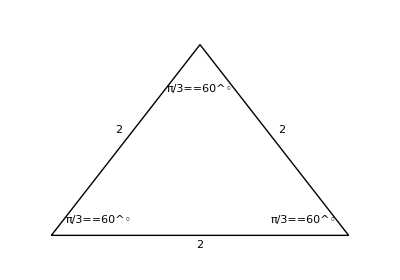

```mathematica
Show[
Graphics[Line[{{0,0},{2,0},{1,1},{0,0}}]],
PlotRange->{{-0.1,2.1},{-0.1,1.1}},
AspectRatio->0.7,
Epilog->{
Style[Text[2,{1,0-0.05}],25],
Style[Text[2,{0.5-0.05,0.5+0.05}],25],
Style[Text[2,{1.5+0.05,0.5+0.05}],25],
Style[Text[HoldForm[Pi/3==60^◦],{0.32,0.08}],14],
Style[Text[HoldForm[Pi/3==60^◦],{1,1-0.23}],14],
Style[Text[HoldForm[Pi/3==60^◦],{2-0.3,0.08}],14]
}]
Export[{"st3.pdf","st3.svg"},%];
```

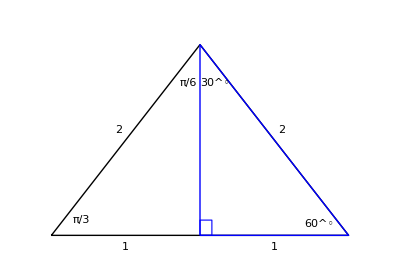

```mathematica
Show[
Graphics[Line[{{0,0},{2,0},{1,1},{0,0}}]],
Graphics[{Blue,Thick,Line[{{1,0},{2,0},{1,1},{1,0}}]}],
Graphics[{Thick,FaceForm[Directive[White,Opacity[0]]],EdgeForm[Blue],Rectangle[{1,0},{1.08,0.08}]}],
PlotRange->{{-0.1,2.1},{-0.1,1.1}},
AspectRatio->0.7,
Epilog->{
Style[Text[1,{1.5,0-0.06}],25],
Style[Text[1,{0.5,0-0.06}],25],
Style[Text[2,{0.5-0.05,0.5+0.05}],25],
Style[Text[2,{1.5+0.05,0.5+0.05}],25],
Style[Text[HoldForm[Pi/3],{0.2,0.08}],14],
Style[Text[HoldForm[30^◦],{1.1,1-0.2}],14],
Style[Text[HoldForm[Pi/6],{1-0.08,1-0.2}],14],
Style[Text[HoldForm[60^◦],{2-0.2,0.06}],14]
}]
Export[{"st4.pdf","st4.svg"},%];
```

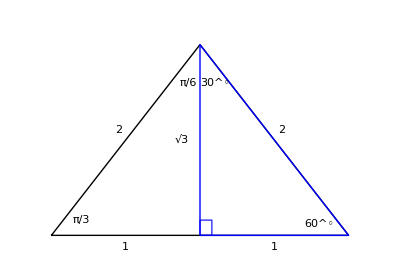

```mathematica
Show[
Graphics[Line[{{0,0},{2,0},{1,1},{0,0}}]],
Graphics[{Blue,Thick,Line[{{1,0},{2,0},{1,1},{1,0}}]}],
Graphics[{Thick,FaceForm[Directive[White,Opacity[0]]],EdgeForm[Blue],Rectangle[{1,0},{1.08,0.08}]}],
PlotRange->{{-0.1,2.1},{-0.1,1.1}},
AspectRatio->0.7,
Epilog->{
Style[Text[Sqrt[3],{1-0.12,0.5}],20],
Style[Text[1,{1.5,0-0.06}],20],
Style[Text[1,{0.5,0-0.06}],20],
Style[Text[2,{0.5-0.05,0.5+0.05}],20],
Style[Text[2,{1.5+0.05,0.5+0.05}],20],
Style[Text[HoldForm[Pi/3],{0.2,0.08}],14],
Style[Text[HoldForm[30^◦],{1.1,1-0.2}],14],
Style[Text[HoldForm[Pi/6],{1-0.08,1-0.2}],14],
Style[Text[HoldForm[60^◦],{2-0.2,0.06}],14]
}]
Export[{"st5.pdf","st5.svg"},%];
```